Exercises for Section 40 | Defining Your Own Functions

Define a function f that computes the square of its argument. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
f[x_]:=x^2
```

```mathematica
Clear[f]
```

Define a function poly that takes an integer, and makes a picture of an orange regular polygon with that number of sides. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
poly[int_]:=Graphics[Style[RegularPolygon[int],Orange]]
```

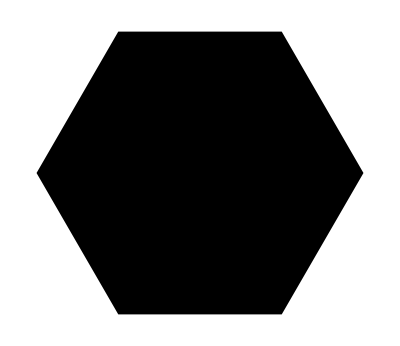

```mathematica
poly[6]
```

```mathematica
Clear[poly]
```

Define a function f that takes a list of two elements and puts them in reverse order. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
elementreverse[one_,two_]:={two,one}
```

```mathematica
elementreverse[1,2]
```

{2,1}

```mathematica
Clear[elementreverse]
```

Create a function f that takes two arguments and gives the result of multiplying them and dividing by their sum. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
f[one_,two_]:={(one*two)/(one+two)}
```

```mathematica
Clear[f]
```

Define a function f that takes a list of two elements and returns a list of their sum, difference and ratio. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
f[one_,two_]:={one+two,one-two,one/two}
```

```mathematica
Clear[f]
```

Define a function evenodd that gives Black if its argument is even and White otherwise, but gives Red if its argument is 0. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
evenodd[x_]:=If[EvenQ[x],Black,White];evenodd[o]=Red;
```

```mathematica
Clear[evenodd]
```

Define a function f of three arguments where the second two arguments are added if the first argument is 1, multiplied if it’s 2 and raised to a power if it’s 3. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
f[1,two_,three_]:=two+three;
f[2,two_,three_]:=two*three;
f[3,two_,three_]:=two^three;
```

```mathematica
Clear[f]
```

Define a Fibonacci function f with f[0] and f[1] both being 1, and f[n] for integer n being the sum of f[n-1] and f[n-2]. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
f[0]=f[1]=1;
f[n_]:=f[n-1]+f[n-2]
```

```mathematica
f/@Range[10]
```

{1,2,3,5,8,13,21,34,55,89}

```mathematica
Clear[f]
```

Create a function animal that takes a string, and gives a picture of an animal with that name. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
animal[str_string]:=Interpreter["Animal"][str]
```

```mathematica
animal[str_] := SemanticInterpretation[ToString[str]]["Image"]
```

```mathematica
animal[lama]
```

-Graphics-

```mathematica
Clear[animal]
```

```mathematica
animal[kind_String]:=Interpreter["Animal"][kind]["Image"]
```

```mathematica
animal[sheep]
```

animal[sheep]

```mathematica
Clear[animal]
```

Define a function nearwords that takes a string and an integer n, and gives the n words in WordList[ ] that are nearest to a given string. |

NO EXPECTED OUTPUT »

Many possible solutions of the form _:=_ or _=_ | ×

```mathematica
nearwords[s_Stirng,n_Integer]:=Nearest[WordList[],s,5]
```

```mathematica
nearwords[program]
```

nearwords[program]

```mathematica
Clear[nearwords]
```